## Definitions

### Screen to Phase Space Mappings

```mathematica
Clear[textureCoordToPixel,pixelToScreen,αβToηλ,rotateSphericalCoordinate,FromSphericalCoordinatesCustom,ToSphericalCoordinatesCustom,normalizeAngle2]
textureCoordToPixel[textureWidth_,textureHeight_][u_,v_]:=Module[{pixelCoords,center},
pixelCoords = {u * textureWidth,v*textureHeight};
center={textureWidth/2.0,textureHeight/2.0};
pixelCoords-center
]
pixelToScreen[x_,y_]:=Module[{base,rcrit,alpha,n,r},
base = 0.04;
rcrit = 300;
alpha = 1000;
n = 1;
r = √(x^2+y^2);
If[r < rcrit,base*{x,y},(1/alpha(r-rcrit)^n+base)*{x,y}]
]
αβToηλ[a_][θs_][α_,β_]:=Module[{},
{(α^2-a^2)*Cos[θs]^2+β^2,-1*α*Sin[θs]}
]
normalizeAngle2[angle_]:=Module[{a=Mod[angle,2 π]},If[a>π,a-2π,a]]
FromSphericalCoordinatesCustom[v_]:=Module[{},
FromSphericalCoordinates[{v[[1]],v[[2]],normalizeAngle2[v[[3]]]}]
]
ToSphericalCoordinatesCustom[v_]:=Module[{vSpherical},
vSpherical=ToSphericalCoordinates[v];
{vSpherical[[1]],vSpherical[[2]],Mod[vSpherical[[3]],2π]}
]
rotateSphericalCoordinate[vs_,vo_]:=Module[{vsCartesian, voCartesian,zhat,n1,v2,n2,n3,voHatCartesian,M},
vsCartesian=FromSphericalCoordinatesCustom[vs];
voCartesian=FromSphericalCoordinatesCustom[vo];

zhat={0,0,1};
n1=vsCartesian/Norm[vsCartesian];

v2=zhat-(zhat.n1) * n1;
n2=If[Norm[v2]==0,{0,1,0},v2/Norm[v2]];

n3=Cross[n2,n1];

M={n1,n3,n2};
voHatCartesian=M.voCartesian;

ToSphericalCoordinatesCustom[voHatCartesian]
]
```

### Radial Functions and Integrals

```mathematica
Clear[Ir,Iϕ,Ipm,mathcalIpm,F2ofr,x2,k,R,Π2ofr]
R[a_,M_][η_,λ_][r_]:=(r^2+a^2-a λ)^2-(r^2-2 M r+a^2)(η+(λ-a)^2);

k[r1_,r2_,r3_,r4_]:=((r3-r2)*(r4-r1))/((r3-r1)*(r4-r2));
x2[r1_,r2_,r3_,r4_][r_]:=√((r-r4)/(r-r3)*(r3-r1)/(r4-r1));
F2ofr[r1_,r2_,r3_,r4_][r_]:=2/(√((r3-r1)*(r4-r2)))*EllipticF[ArcSin[x2[r1,r2,r3,r4][r]],k[r1,r2,r3,r4]]

Π2ofr[isPlus_][a_,M_][r1_,r2_,r3_,r4_][r_]:=Module[{rplus,rminus,rpm3,rpm4,t1,t2,t3,n},
rplus=M+√(M^2-a^2);
rminus=M-√(M^2-a^2);

rpm3=If[isPlus,rplus-r3,rminus-r3];
rpm4=If[isPlus,rplus-r4,rminus-r4];

t1=2/(√((r3-r1)(r4-r2)));
t2=(r4-r3)/(rpm3*rpm4);

n=(rpm3*(r4-r1))/(rpm4(r3-r1));
t3=EllipticPi[n,ArcSin[x2[r1,r2,r3,r4][r]],k[r1,r2,r3,r4]];

t1*t2*t3
]

Ir[r1_,r2_,r3_,r4_][ro_,rs_]:=F2ofr[r1,r2,r3,r4][ro]+F2ofr[r1,r2,r3,r4][rs]

mathcalIpm[isPlus_][a_,M_][r1_,r2_,r3_,r4_][r_]:=Module[{rplus, rminus, t1,t2},
rplus=M+√(M^2-a^2);
rminus=M-√(M^2-a^2);

t1=If[isPlus,-Π2ofr[True][a,M][r1,r2,r3,r4][r],-Π2ofr[False][a,M][r1,r2,r3,r4][r]];
t2=If[isPlus,-F2ofr[r1,r2,r3,r4][r]/(rplus-r3),-F2ofr[r1,r2,r3,r4][r]/(rminus-r3)];

t1+t2
]

Ipm[isPlus_][a_,M_][r1_,r2_,r3_,r4_][ro_,rs_]:=Module[{mathcalIpmatro,mathcalIpmatrs},
mathcalIpmatro=mathcalIpm[isPlus][a,M][r1,r2,r3,r4][ro];
mathcalIpmatrs=mathcalIpm[isPlus][a,M][r1,r2,r3,r4][rs];

mathcalIpmatro + mathcalIpmatrs
]

Iϕ[a_,M_][η_,λ_][r1_,r2_,r3_,r4_][ro_,rs_]:=Module[{Iplus,Iminus,rplus,rminus,t1,t2},
rplus=M+√(M^2-a^2);
rminus=M-√(M^2-a^2);

Iplus=Ipm[True][a,M][r1,r2,r3,r4][ro,rs];
Iminus=Ipm[False][a,M][r1,r2,r3,r4][ro,rs];

t1=rplus-(a λ)/(2 M);
t2=rminus-(a λ)/(2 M);

(2a M)/(rplus-rminus)(t1*Iplus-t2*Iminus)
]



ObtainRadialRoots[a_,M_][η_,λ_]:=Module[{roots},
roots=Solve[R[a,M][η,λ][r]==0,r];
roots=r/.roots//Chop;
Sort[roots]
]
```

### Angular Functions and Integrals

```mathematica
Clear[Δθ,uplus,uminus];
Δθ[a_][η_,λ_]:=1/2(1-(η+λ^2)/a^2);
uplus[a_][η_,λ_]:=Δθ[a][η,λ]+√((Δθ[a][η,λ])^2+η/a^2);
uminus[a_][η_,λ_]:=Δθ[a][η,λ]-√((Δθ[a][η,λ])^2+η/a^2);
```

```mathematica
Clear[mathcalGθ,mathcalGϕ]
mathcalGθ[a_][η_,λ_][θ_]:=-1/(√(-uminus[a][η,λ]*a^2))EllipticF[ArcSin[Cos[θ]/(√(uplus[a][η,λ]))],(uplus[a][η,λ])/(uminus[a][η,λ])]
mathcalGϕ[a_][η_,λ_][θ_]:=-1/(√(-uminus[a][η,λ]*a^2))EllipticPi[uplus[a][η,λ],ArcSin[Cos[θ]/(√(uplus[a][η,λ]))],(uplus[a][η,λ])/(uminus[a][η,λ])]
```

```mathematica
Clear[Ψτ,Gϕ,ellipticP,CosθObserver]
Ψτ[a_][η_,λ_,θs_][τ_,νθ_]:=JacobiAmplitude[√(-uminus[a][η,λ]*a*a)(τ+νθ*mathcalGθ[a][η,λ][θs]),(uplus[a][η,λ])/(uminus[a][η,λ])];

Gϕ[DEBUG_][a_][η_,λ_,θs_][τ_,νθ_]:=Module[{t1,t2,t3},
t1=1/(√(-uminus[a][η,λ]*a^2));
If[DEBUG,Print["Gϕ t1 = ", t1]];

t2=EllipticPi[uplus[a][η,λ],Ψτ[a][η,λ,θs][τ,νθ],(uplus[a][η,λ])/(uminus[a][η,λ])];
If[DEBUG,Print["Ψτ = ", Ψτ[a][η,λ,θs][τ,νθ]]];
If[DEBUG,Print["uplus = ",uplus[a][η,λ] ]];
If[DEBUG,Print["uplus / uminus = ", (uplus[a][η,λ])/(uminus[a][η,λ])]];
If[DEBUG,Print["Gϕ EllipticPi = ", t2]];

t3=-νθ*mathcalGϕ[a][η,λ][θs];
If[DEBUG,Print["mathcalGϕ = ", t3]];

t1*t2+t3
]

ellipticP[a_][η_,λ_,θs_][τ_,νθ_]:=EllipticPi[uplus[a][η,λ],Ψτ[a][η,λ,θs][τ,νθ],(uplus[a][η,λ])/(uminus[a][η,λ])];

CosθObserver[a_][η_,λ_,νθs_,θs_][τ_]:=Module[{mathcalGθs,u,m},
mathcalGθs=mathcalGθ[a][η,λ][θs];
u=√(-1*uminus[a][η,λ]*a^2)*(τ+νθs*mathcalGθs);
m=(uplus[a][η,λ])/(uminus[a][η,λ]);
-1*νθs*√(uplus[a][η,λ])JacobiSN[u,m]
]
```

## Computing the Lensing Map

```mathematica
Clear[kerrLense]
kerrLense[DEBUG_][a_,M_][η_,λ_][θs_,νθs_,ro_,rs_]:=Module[{r1,r2,r3,r4,cosθf,ϕf,ERRORSTRING,IrValue,τ,rplus,cosθo,GϕValue,IϕValue},
cosθf=-1.0;
ϕf=-1.0;
ERRORSTRING="FAILURE";

(* Obtain the roots *)
{r1,r2,r3,r4}=ObtainRadialRoots[a,M][η,λ];
If[DEBUG,Print["r1 = ",r1,", r2 = ",r2,", r3 = ",r3,", r4 = ",r4]];

(* If any are complex return *)
If[AnyTrue[{r1,r2,r3,r4},Im[#]!=0&],Return[{-1.0,-1.0,"COMPLEX ROOTS"}]];

(* Make sure in correct subcase of (2) *)
rplus=M+√(M^2-a^2);
If[r4<rplus,Return[{-1.0,-1.0,"EMITTED FROM BLACK HOLE"}]];

IrValue=Ir[r1,r2,r3,r4][ro,rs];
If[DEBUG,Print["Ir = ",IrValue]];

τ=IrValue;

cosθo=CosθObserver[a][η,λ,νθs,θs][τ];
If[DEBUG,Print["cos(θ_o) = ",cosθo]];

GϕValue=Gϕ[DEBUG][a][η,λ,θs][τ,νθs];
If[DEBUG,Print["Gϕ = ",GϕValue]];

IϕValue=Iϕ[a,M][η,λ][r1,r2,r3,r4][ro,rs];
If[DEBUG,Print["Iϕ = ",IϕValue]];

cosθf=cosθo;
ϕf=IϕValue+λ*GϕValue;
ERRORSTRING="SUCCESS";
{cosθf,ϕf,ERRORSTRING}
]
```

```mathematica
Clear[kerrLenseTextureCoordinate]
kerrLenseTextureCoordinate[DEBUG_][a_,M_,θs_,ro_,rs_][u_,v_]:=Module[{textureWidth,textureHeight,i,j,α,β,η,λ,νθs,cosθf,θf,ϕf,ERRORSTRING,rotatedSphericalCoordinates,ϕfNormalized,oneTwoBdd,threeFourBdd,vpp,upp,vp,up,TEXTURE,vCoordSpacing,uCoordSpacing},
vCoordSpacing=1/height;
uCoordSpacing=1/width;
vpp=If[v==1/2,v+(1/2)vCoordSpacing,v];
upp=If[u==1/2,u+(1/2)uCoordSpacing,u];

{i,j}=textureCoordToPixel[1920,1080][upp,vpp];
If[DEBUG,Print["i = ",i," j = ", j]];

{α,β}=pixelToScreen[j,i];
If[DEBUG,Print["α = ",α," β = ",β]];

{η,λ}=αβToηλ[a][π/2][α,β];
If[DEBUG,Print["η = ", η, " λ = ", λ]];


νθs=If[β==0,1,Sign[β]];
If[DEBUG,Print["νθ = ",νθs]];

{cosθf,ϕf,ERRORSTRING}=kerrLense[DEBUG][a,M][η,λ][θs,νθs,ro,rs];
If[DEBUG,Print["cosθf = ", cosθf, " ϕf = ", ϕf, " Error string = ", ERRORSTRING]];
If[ERRORSTRING!="SUCCESS",Return[{-1,-1,"FAILURE"}]];

θf=ArcCos[cosθf];

rotatedSphericalCoordinates=rotateSphericalCoordinate[{rs,θs,0.0},{ro,θf,ϕf}];
If[DEBUG,Print["rotated spherical coordinates = ", rotatedSphericalCoordinates]];

ϕfNormalized=Mod[rotatedSphericalCoordinates[[3]],2π];
θf=rotatedSphericalCoordinates[[2]];

oneTwoBdd=π/2;
threeFourBdd=3 π/2;

vp=θf/π;
up=0;
TEXTURE="";
If[0<=ϕfNormalized<=oneTwoBdd,
up=1/2+1/2*(ϕfNormalized/oneTwoBdd);
TEXTURE="FRONT TEXTURE";,
If[threeFourBdd<=ϕfNormalized<=2π,
up=1/2*((ϕfNormalized-threeFourBdd)/(2 π-threeFourBdd));
TEXTURE="FRONT TEXTURE";,
up=(ϕfNormalized-oneTwoBdd)/(threeFourBdd-oneTwoBdd);
TEXTURE="BACK TEXTURE";]
];

{vp,up,TEXTURE}
]
```

```mathematica
astar=0.2;
Mstar=1;
θsstar=π/2;
rostar=1000;
rsstar=1000;
width=1920;
height=1080;
kerrLenseTextureCoordinate[True][astar,Mstar,θsstar,rostar,rsstar][700/width,543/height]
```

i = -260. j = 3.

α = 0.12 β = -10.4

η = 108.16 λ = -0.12

νθ = -1

r1 = -11.2852, r2 = 0.0201845, r3 = 2.06434, r4 = 9.20064

Ir = 0.35351

cos(θ_o) = -0.510199

Gϕ t1 = 0.0961474

Ψτ = 3.67705

uplus = 0.999867

uplus / uminus = -0.000369724

Gϕ EllipticPi = 272.883

mathcalGϕ = 0.

Gϕ = 26.237

Iϕ = 0.0120711

cosθf = -0.510199 ϕf = -3.13637 Error string = SUCCESS

rotated spherical coordinates = {1000.,2.10621,3.14681}

{0.670428,0.501661,BACK TEXTURE}

uplus / uminus = -0.000369724

Gϕ EllipticPi = 272.883

mathcalGϕ = 0.

Gϕ = 26.237

Iϕ = 0.0120711

cosθf = -0.510199 ϕf = -3.13637 Error string = SUCCESS

rotated spherical coordinates = {1000.,2.10621,3.14681}

{0.670428,0.501661,BACK TEXTURE}

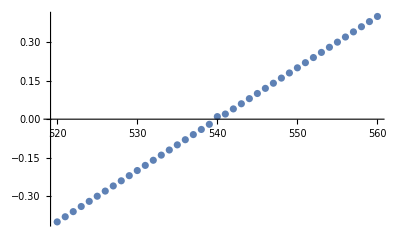

```mathematica
col=700;
Table[{i,textureToAlpha[col/width,i/height]},{i,520,560}];
ListPlot[%]
```

```mathematica
540/height
```

1/2

$Aborted

```mathematica
lutTexture[[1]]
```

{0.185347,0.900838,FRONT TEXTURE}

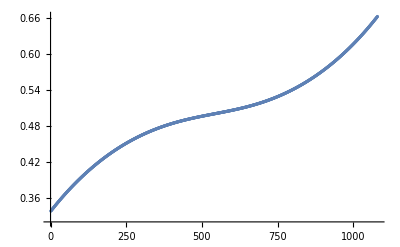

```mathematica
ListPlot[lutTexture[[;;,2]]]
```

```mathematica
astar=0.9;
Mstar=1;
θsstar=π/2;
rostar=1000;
rsstar=1000;
width=1920;
height=1080;

col=9;
row=541;
kerrLenseTextureCoordinate[True][astar,Mstar,θsstar,rostar,rsstar][col/width,row/height]
```

i = -951. j = 1.

α = 0.691001 β = -657.141

η = 431835. λ = -0.691001

νθ = -1

r1 = -658.14, r2 = 0.564102, r3 = 1.43592, r4 = 656.14

Ir = 0.00260813

cos(θ_o) = 0.989776

Gϕ t1 = 0.00152174

Ψτ = 1.71391

uplus = 0.999999

uplus / uminus = -1.87571×10^-6

Gϕ EllipticPi = 2980.7

mathcalGϕ = 0.

Gϕ = 4.53586

Iϕ = 6.33433×10^-6

cosθf = 0.989776 ϕf = -3.13427 Error string = SUCCESS

rotated spherical coordinates = {1000.,0.143118,3.14891}

{0.0455557,0.50233,BACK TEXTURE}

## Series Expansion

```mathematica
dd+√(dd^2(1+ϵ));
Series[%,{ϵ,0,4}]

dd-√(dd^2(1+ϵ));
Series[%,{ϵ,0,4}]
```

## Texture Export

```mathematica
SetDirectory@NotebookDirectory[]
```

```mathematica
astar=0.999;
Mstar=1;
θsstar=π/2;
rostar=1000;
rsstar=1000;
width=1920;
height=1080;
col=500;
lutTexture=ParallelTable[
kerrLenseTextureCoordinate[False][astar,Mstar,θsstar,rostar,rsstar][col/width,row/height]
,{col,1,width},{row,1,height}
];
mmamatrix=Table[Join[lutTexture[[i,j]][[1;;2]],If[lutTexture[[i,j]][[3]]=="FRONT TEXTURE",{0, 1},If[lutTexture[[i,j]][[3]]=="BACK TEXTURE",{0, 0},{1,0}]]],{i,1,Length[lutTexture]},{j,1,Length[lutTexture[[1]]]}];
```

```mathematica
(* Data verification *)
Length[mmamatrix]
Length[mmamatrix[[1]]]
Length[mmamatrix[[1]][[1]]]

mmamatrix[[1,1;;10]]
```

1920

1080

4

{{0.287356,0.646261,0,1},{0.286017,0.647334,0,1},{0.284688,0.648403,0,1},{0.283369,0.649467,0,1},{0.282059,0.650527,0,1},{0.28076,0.651583,0,1},{0.279469,0.652635,0,1},{0.278188,0.653683,0,1},{0.276916,0.654727,0,1},{0.275654,0.655767,0,1}}

```mathematica
(* Export the data to csv *)
matrix=mmamatrix;
flatMatrix=Flatten[matrix,1];
Export["data-verification/mma/lut-texture-a-0-999.csv",flatMatrix,"CSV"]
```

data-verification/mma/lut-texture-a-0-999.csv

## Scratch Section

```mathematica
Clear[textureToAlpha]
textureToAlpha[u_,v_]:=Module[{textureWidth,textureHeight,i,j,α,β,η,λ,νθs,cosθf,θf,ϕf,ERRORSTRING,rotatedSphericalCoordinates,ϕfNormalized,oneTwoBdd,threeFourBdd,vp,up,TEXTURE,vCoordSpacing},
vCoordSpacing=1/height;
vp=If[v==1/2,v+(1/2)vCoordSpacing,v];
{i,j}=textureCoordToPixel[1920,1080][u,vp];
{α,β}=pixelToScreen[j,i];
α
]
```

```mathematica
SetDirectory@NotebookDirectory[]
```

/home/graveltr/Nextcloud

data-verification/mma/lut-texture-a-0-5.csv